```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/dj/Flypes/src

## Testing

```mathematica
<<KnotTheory`
```

Loading KnotTheory` version of September 6, 2014, 13:37:37.2841.
Read more at http://katlas.org/wiki/KnotTheory.

```mathematica
ImportPythonResultsCSV[filepath_]:=Module[{fileToVerify,numCrossings,pdCodes},
fileToVerify=Import[filepath,"CSV"];
numCrossings=fileToVerify⟦1⟧;
Return[ReplacePDCode/@Partition[fileToVerify⟦2;;Length[fileToVerify]⟧,numCrossings]];
]
```

```mathematica
ImportPythonResultsTxt[filepath_]:=Module[{fileToVerify},
fileToVerify=StringSplit[Import[filepath,"Plaintext"],"\n"];
Return[ToExpression/@fileToVerify⟦2;;Length[fileToVerify]⟧];
]
```

```mathematica
k13crossingNumberOfOutputs=Table[Length[ImportPythonResultsTxt["/Users/dj/Flypes/flype_output/13_crossing/knot_13_"<>ToString[i]<>"_output.txt"]],{i,NumberOfKnots[13,Alternating]}];
```

```mathematica
Max[k13crossingNumberOfOutputs]
```

192

```mathematica
Total[k13crossingNumberOfOutputs]
```

53413

```mathematica
k12crossingNumberOfOutputs=Table[Length[GetAllMinimalPDCodes[Knot[12,Alternating,i]]],{i,NumberOfKnots[12,Alternating]}];
```

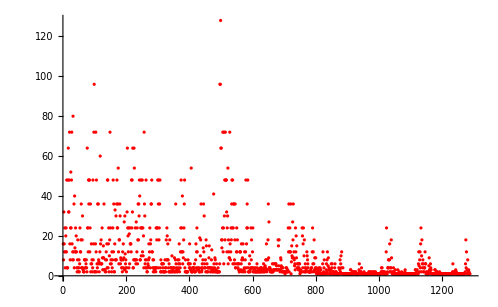

```mathematica
k12crossingPlot=ListPlot[k12crossingNumberOfOutputs,PlotRange->{0,Max[k12crossingNumberOfOutputs]},PlotStyle->Red]
```

```mathematica
Total[#⟦2⟧&/@Sort[Tally[k13crossingNumberOfOutputs]]]
```

4878

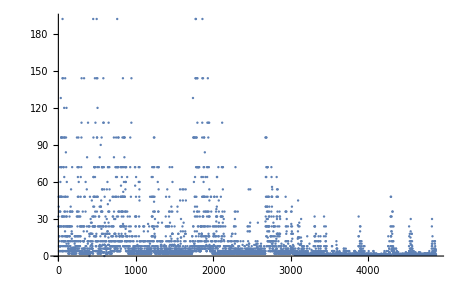

```mathematica
k13crossingPlot=ListPlot[k13crossingNumberOfOutputs,PlotRange->{0,Max[k13crossingNumberOfOutputs]}]
```

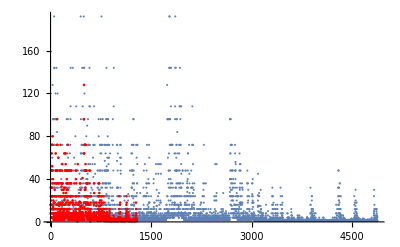

```mathematica
Show[k13crossingPlot,k12crossingPlot]
```

```mathematica
maxNumberOfMinimalDiagrams=Union[
Table[
Max[
Table[Length[GetAllMinimalPDCodes[Knot[i,j]]],{j,NumberOfKnots[i,Alternating]}]
],{i,3,10}
],
Table[
Max[
Table[Length[GetAllMinimalPDCodes[Knot[i,Alternating,j]]],{j,NumberOfKnots[i,Alternating]}]
],{i,11,12}
],
{192}
]
```

{1,2,3,6,12,32,48,128,192}

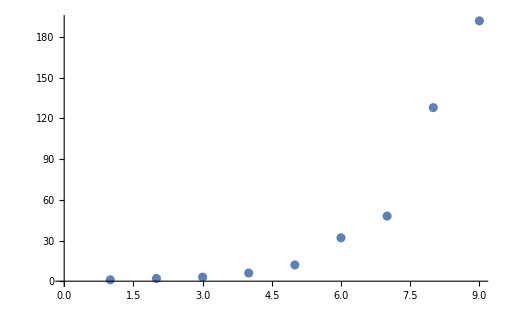

```mathematica
ListPlot[maxNumberOfMinimalDiagrams]
```

```mathematica
Table[
Table[Length[GetAllMinimalPDCodes[Knot[i,j]]],{j,NumberOfKnots[i,Alternating]}],{i,3,10}
]
```

{{1},{1},{1,1},{1,1,2},{1,1,1,1,2,3,2},{1,1,1,1,1,2,2,4,2,2,3,5,4,6,3,1,1,1},{1,1,1,1,2,2,3,5,2,2,3,3,4,4,6,2,4,6,8,6,6,4,5,6,6,8,12,7,1,8,8,2,2,1,1,3,2,1,1,1,1},{1,1,1,1,2,2,3,1,2,4,2,4,5,6,4,3,2,6,4,3,5,4,8,6,9,6,12,8,9,12,8,12,8,6,8,10,8,12,12,18,18,24,18,24,32,1,2,2,4,3,6,4,8,4,8,6,12,6,12,10,1,2,3,1,4,4,3,2,8,9,18,12,24,3,4,4,12,14,1,2,4,1,2,3,1,2,3,4,4,1,1,2,1,1,2,2,2,1,1,1,2,1,1,1,2,1,2,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1}}

```mathematica
VerifyPythonFlypeResults[filepath_,knot_]:=Module[{numCrossings,fileToVerify,pdCodes,mathematicaPdCodes},
fileToVerify=Import[filepath,"CSV"];
numCrossings=fileToVerify⟦1⟧;
pdCodes=ImportPythonResultsCSV[filepath];

mathematicaPdCodes=PerformAllFlypes[PD@Knot[8,14]];

(* If lengths are different, then it's definitely not right *)
If[Length[pdCodes]≠Length[mathematicaPdCodes],Return[False]];

Print[Sort@(Sort/@pdCodes)];
Print[Sort@(Sort/@ReplacePDCode/@mathematicaPdCodes)];

Print[Sort@(Sort/@pdCodes)==Sort@(Sort/@ReplacePDCode/@mathematicaPdCodes)];

]
```

```mathematica
GetAllMinimalPDCodes[Knot[8,14]]
```

{PD[X[1,4,2,5],X[13,16,14,1],X[11,3,12,2],X[3,11,4,10],X[5,12,6,13],X[9,6,10,7],X[7,14,8,15],X[15,8,16,9]],PD[X[1,4,2,5],X[7,1,8,16],X[11,2,12,3],X[3,12,4,13],X[5,14,6,15],X[9,6,10,7],X[15,9,16,8],X[13,10,14,11]],PD[X[7,16,8,1],X[1,10,2,11],X[11,2,12,3],X[3,6,4,7],X[15,5,16,4],X[5,15,6,14],X[13,8,14,9],X[9,12,10,13]],PD[X[1,6,2,7],X[9,1,10,16],X[5,2,6,3],X[3,12,4,13],X[13,4,14,5],X[7,14,8,15],X[11,8,12,9],X[15,11,16,10]],PD[X[1,4,2,5],X[11,16,12,1],X[9,3,10,2],X[3,9,4,8],X[5,10,6,11],X[13,6,14,7],X[7,14,8,15],X[15,12,16,13]],PD[X[5,1,6,16],X[1,10,2,11],X[11,2,12,3],X[3,14,4,15],X[7,4,8,5],X[15,7,16,6],X[13,8,14,9],X[9,12,10,13]]}

```mathematica
ExportPDAsPythonTxt[path_,crNum_,entry_]:=Module[{},
Export[path<>"knot_"<>ToString[crNum]<>"_"<>ToString[entry]<>".txt",RemovePDCode@PD@Knot[crNum,Alternating,entry]];
]
```

```mathematica
Export["/Users/dj/Flypes/knot_txt_files/particular_example.txt",{{32,2,33,1},{2,8,3,7},{30,3,31,4},{4,36,5,35},{28,6,29,5},{6,33,7,34},{8,32,9,31},{36,9,37,10},{10,37,11,38},{38,11,39,12},{12,19,13,20},{26,14,27,13},{14,22,15,21},{42,16,1,15},{16,23,17,24},{40,17,41,18},{18,26,19,25},{20,27,21,28},{22,41,23,42},{24,40,25,39},{34,30,35,29}}]
```

/Users/dj/Flypes/knot_txt_files/particular_example.txt

```mathematica
Do[ExportPDAsPythonTxt["/Users/dj/Flypes/knot_txt_files/",13,i],{i,NumberOfKnots[13,Alternating]}]
```

KnotTheory::loading: Loading precomputed data in KnotTheory/13A.dts.

KnotTheory::credits: The GaussCode to PD conversion was written by Siddarth Sankaran at the University of Toronto in the summer of 2005.

```mathematica
NumberOfKnots[#,Alternating]&/@{9,10,11,12,13}
```

{41,123,367,1288,4878}

## Absolute Confusion

```mathematica
python814List={
PD[X[4,1,5,2],X[16,13,1,14],X[2,12,3,11],X[10,4,11,3],X[12,5,13,6],X[6,9,7,10],X[14,7,15,8],X[8,15,9,16]],PD[X[10,1,11,2],X[16,13,1,14],X[2,5,3,6],X[12,4,13,3],X[4,12,5,11],X[6,9,7,10],X[14,7,15,8],X[8,15,9,16]],PD[X[1,8,2,9],X[11,16,12,1],X[5,2,6,3],X[3,11,4,10],X[9,5,10,4],X[13,6,14,7],X[7,14,8,15],X[15,12,16,13]],PD[X[16,10,1,9],X[14,1,15,2],X[2,11,3,12],X[8,3,9,4],X[4,7,5,8],X[12,5,13,6],X[6,13,7,14],X[10,16,11,15]],PD[X[1,4,2,5],X[11,16,12,1],X[9,3,10,2],X[3,9,4,8],X[5,10,6,11],X[13,6,14,7],X[7,14,8,15],X[15,12,16,13]]
};
```

```mathematica
sortedPythonCodes814=Sort@(Sort/@python814List)
```

{PD[X[1,4,2,5],X[3,9,4,8],X[5,10,6,11],X[7,14,8,15],X[9,3,10,2],X[11,16,12,1],X[13,6,14,7],X[15,12,16,13]],PD[X[1,8,2,9],X[3,11,4,10],X[5,2,6,3],X[7,14,8,15],X[9,5,10,4],X[11,16,12,1],X[13,6,14,7],X[15,12,16,13]],PD[X[2,5,3,6],X[4,12,5,11],X[6,9,7,10],X[8,15,9,16],X[10,1,11,2],X[12,4,13,3],X[14,7,15,8],X[16,13,1,14]],PD[X[2,11,3,12],X[4,7,5,8],X[6,13,7,14],X[8,3,9,4],X[10,16,11,15],X[12,5,13,6],X[14,1,15,2],X[16,10,1,9]],PD[X[2,12,3,11],X[4,1,5,2],X[6,9,7,10],X[8,15,9,16],X[10,4,11,3],X[12,5,13,6],X[14,7,15,8],X[16,13,1,14]]}

```mathematica
sortedAllCodesFor814=Sort@(Sort/@GetAllMinimalPDCodes[Knot[8,14]])
```

{PD[X[1,4,2,5],X[3,9,4,8],X[5,10,6,11],X[7,14,8,15],X[9,3,10,2],X[11,16,12,1],X[13,6,14,7],X[15,12,16,13]],PD[X[1,4,2,5],X[3,11,4,10],X[5,12,6,13],X[7,14,8,15],X[9,6,10,7],X[11,3,12,2],X[13,16,14,1],X[15,8,16,9]],PD[X[1,4,2,5],X[3,12,4,13],X[5,14,6,15],X[7,1,8,16],X[9,6,10,7],X[11,2,12,3],X[13,10,14,11],X[15,9,16,8]],PD[X[1,6,2,7],X[3,12,4,13],X[5,2,6,3],X[7,14,8,15],X[9,1,10,16],X[11,8,12,9],X[13,4,14,5],X[15,11,16,10]],PD[X[1,10,2,11],X[3,6,4,7],X[5,15,6,14],X[7,16,8,1],X[9,12,10,13],X[11,2,12,3],X[13,8,14,9],X[15,5,16,4]],PD[X[1,10,2,11],X[3,14,4,15],X[5,1,6,16],X[7,4,8,5],X[9,12,10,13],X[11,2,12,3],X[13,8,14,9],X[15,7,16,6]]}

```mathematica
PDMemberQ[list_,pdcode_]:=Module[{i,tempPDcode=RemovePDCode@pdcode,n=Length@pdcode},
(*Print[tempPDcode];
Print[list];*)
For[i=1,i≤2*n,i++,
If[MemberQ[list,ReplacePDCode@tempPDcode],Return[True]];
tempPDcode=Sort@(Mod[#,2*n,1]&/@(#+i*{1,1,1,1})&/@tempPDcode);
(*Print[tempPDcode];*)
];
Return[False];
]
```

```mathematica
Table[PDMemberQ[sortedAllCodesFor814,sortedPythonCodes814⟦i⟧],{i,5}]
```

{True,True,False,True,False}

```mathematica
Table[PDMemberQ[sortedPythonCodes814,sortedAllCodesFor814⟦i⟧],{i,6}]
```

{True,False,False,True,True,False}

```mathematica
Union[GetMinimalLexicographicPDCode/@sortedPythonCodes814]
```

{{{1,4,2,5},{3,9,4,8},{5,10,6,11},{7,14,8,15},{9,3,10,2},{11,16,12,1},{13,6,14,7},{15,12,16,13}},{{1,4,2,5},{3,10,4,11},{5,12,6,13},{7,15,8,14},{9,2,10,3},{11,8,12,9},{13,16,14,1},{15,7,16,6}},{{1,4,2,5},{3,10,4,11},{5,16,6,1},{7,13,8,12},{9,2,10,3},{11,14,12,15},{13,7,14,6},{15,8,16,9}}}

```mathematica
ImportPythonResultsTxt["/Users/dj/Flypes/knot_txt_files/knot_8_14_output.txt"]
```

{PD[X[4,1,5,2],X[16,13,1,14],X[2,12,3,11],X[10,4,11,3],X[12,5,13,6],X[6,9,7,10],X[14,7,15,8],X[8,15,9,16]],PD[X[10,1,11,2],X[16,13,1,14],X[2,5,3,6],X[12,4,13,3],X[4,12,5,11],X[6,9,7,10],X[14,7,15,8],X[8,15,9,16]],PD[X[1,8,2,9],X[11,16,12,1],X[5,2,6,3],X[3,11,4,10],X[9,5,10,4],X[13,6,14,7],X[7,14,8,15],X[15,12,16,13]],PD[X[16,10,1,9],X[14,1,15,2],X[2,11,3,12],X[8,3,9,4],X[4,7,5,8],X[12,5,13,6],X[6,13,7,14],X[10,16,11,15]],PD[X[1,4,2,5],X[11,16,12,1],X[9,3,10,2],X[3,9,4,8],X[5,10,6,11],X[13,6,14,7],X[7,14,8,15],X[15,12,16,13]]}

```mathematica
totalResults=0;
For[i=1,i≤18,i++,
totalResults+=Length[Union[GetMinimalLexicographicPDCode/@ImportPythonResultsTxt["/Users/dj/Flypes/knot_txt_files/knot_8_"<>ToString[i]<>"_output.txt"]]];
]
totalResults
```

34

```mathematica
Table[Length[ImportPythonResultsTxt["/Users/dj/Flypes/knot_txt_files/knot_8_"<>ToString[i]<>"_output.txt"]],{i,18}]
Table[Length[Union[GetMinimalLexicographicPDCode/@ImportPythonResultsTxt["/Users/dj/Flypes/knot_txt_files/knot_8_"<>ToString[i]<>"_output.txt"]]],{i,18}]
```

{1,1,1,1,1,2,2,4,2,2,3,5,4,6,3,1,1,1}

{1,1,1,1,1,2,2,3,2,2,3,5,2,3,2,1,1,1}

```mathematica
(* Issues: 8, 13, 15 *)
```

```mathematica
Table[Length[GetAllMinimalPDCodes[Knot[8,i]]],{i,18}]
Table[Length[Union[GetMinimalLexicographicPDCode/@GetAllMinimalPDCodes[Knot[8,i]]]],{i,18}]
```

{1,1,1,1,1,2,2,4,2,2,3,5,4,6,3,1,1,1}

{1,1,1,1,1,2,2,4,2,2,3,5,4,3,3,1,1,1}

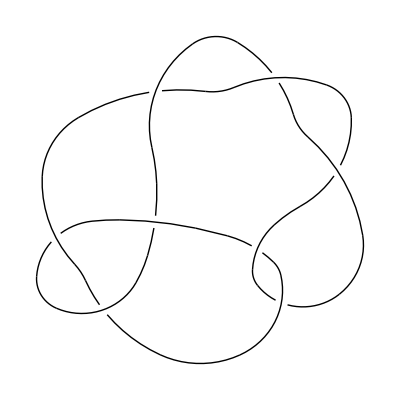

```mathematica
DrawPD[Knot[8,8],{Gap->0.03}]
```

## 8_8 Investigation

```mathematica
python88results=ImportPythonResultsTxt["/Users/dj/Flypes/knot_txt_files/knot_8_"<>ToString[8]<>"_output.txt"]
```

{PD[X[4,1,5,2],X[16,12,1,11],X[2,9,3,10],X[10,3,11,4],X[8,6,9,5],X[6,14,7,13],X[14,8,15,7],X[12,16,13,15]],PD[X[1,4,2,5],X[13,1,14,16],X[11,2,12,3],X[3,12,4,13],X[5,11,6,10],X[9,7,10,6],X[7,15,8,14],X[15,9,16,8]],PD[X[1,4,2,5],X[9,1,10,16],X[7,2,8,3],X[3,8,4,9],X[5,13,6,12],X[13,7,14,6],X[15,11,16,10],X[11,15,12,14]],PD[X[1,6,2,7],X[9,1,10,16],X[7,2,8,3],X[3,13,4,12],X[13,5,14,4],X[5,8,6,9],X[15,11,16,10],X[11,15,12,14]]}

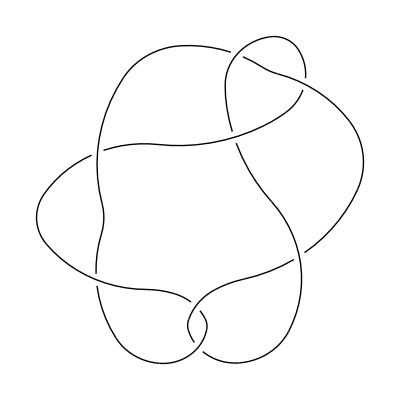
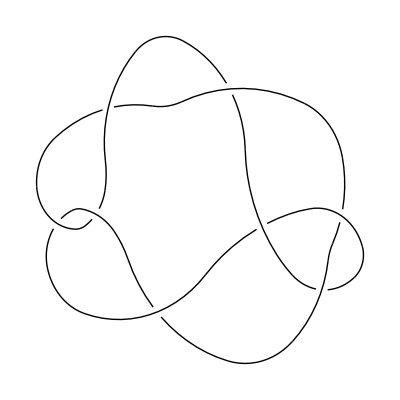
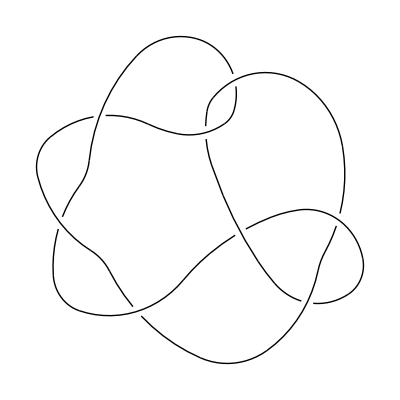
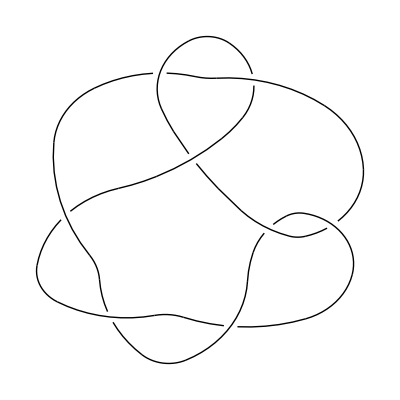

```mathematica
DrawPD[#,{Gap->0.03}]&/@python88results
```

```mathematica
DrawPD[PD@Knot[8,8],{Gap->0.03}]
```

-Graphics-

```mathematica
{DrawPD[python88results⟦1⟧,{Gap->0.03}],Rotate[DrawPD[python88results⟦2⟧,{Gap->0.03}],1]}
```

{-Graphics-,-Graphics-}

```mathematica
DrawPD[#,{Gap->0.03}]&@GetAllMinimalPDCodes[Knot[8,8]]⟦1⟧
```

$Aborted

```mathematica
GetMinimalLexicographicPDCode@GetAllMinimalPDCodes[Knot[8,8]]⟦1⟧
```

{{1,4,2,5},{3,12,4,13},{5,11,6,10},{7,15,8,14},{9,7,10,6},{11,2,12,3},{13,1,14,16},{15,9,16,8}}

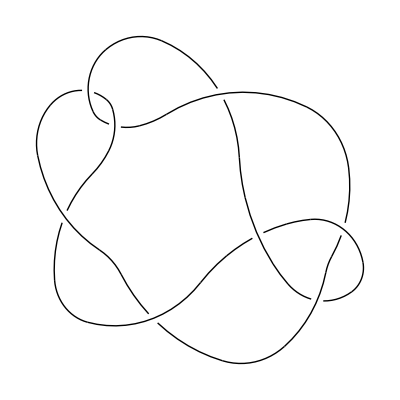

```mathematica
DrawPD[#,{Gap->0.03}]&@GetAllMinimalPDCodes[Knot[8,8]]⟦2⟧
```

```mathematica
DrawPD[#,{Gap->0.03}]&@GetAllMinimalPDCodes[Knot[8,8]]⟦3⟧
```

-Graphics-

```mathematica
DrawPD[#,{Gap->0.03}]&@GetAllMinimalPDCodes[Knot[8,8]]⟦4⟧
```

-Graphics-

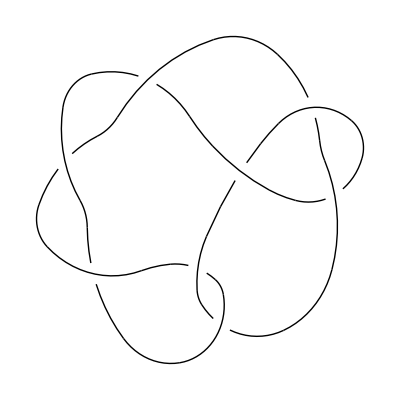
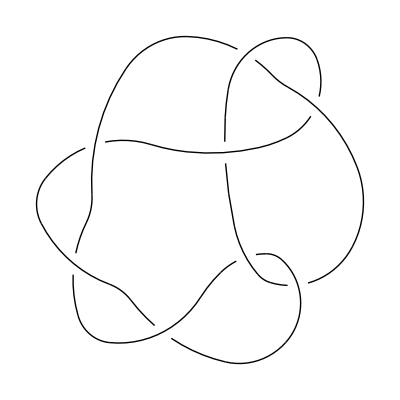
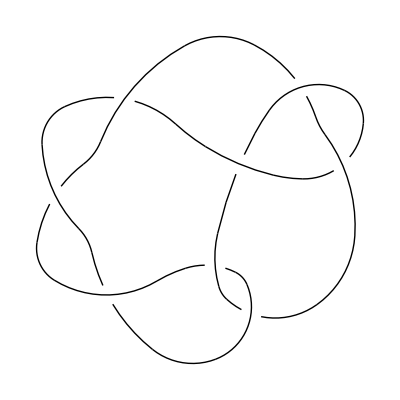
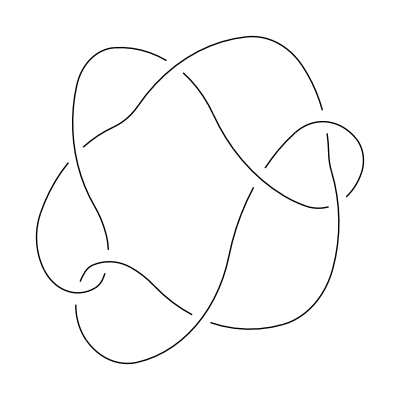
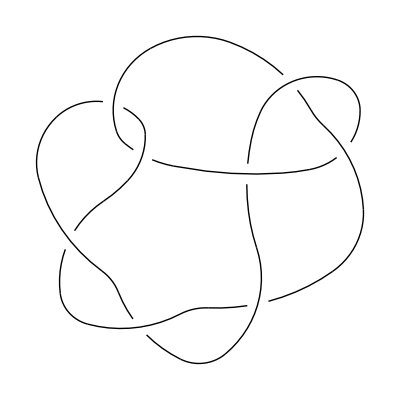
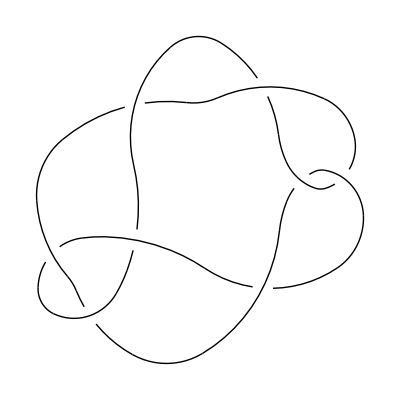
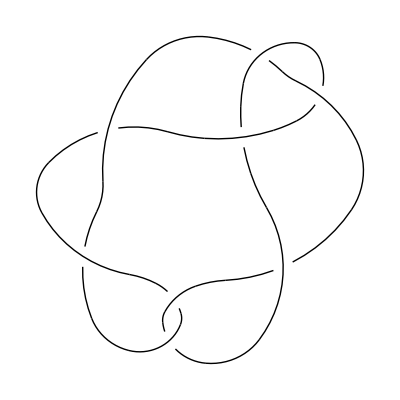
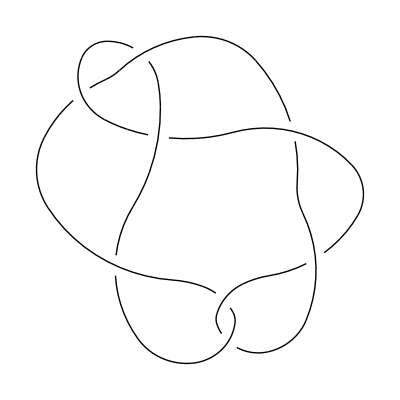
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
DrawPD[#,{Gap->0.05}]&/@{
PD[X[1,6,2,7],X[3,16,4,1],X[5,13,6,12],X[7,2,8,3],X[9,15,10,14],X[11,5,12,4],X[13,11,14,10],X[15,9,16,8]],
PD[X[1,11,2,10],X[3,8,4,9],X[5,2,6,3],X[7,15,8,14],X[9,4,10,5],X[11,1,12,16],X[13,7,14,6],X[15,13,16,12]],
PD[X[1,6,2,7],X[3,13,4,12],X[5,8,6,9],X[7,2,8,3],X[9,1,10,16],X[11,15,12,14],X[13,5,14,4],X[15,11,16,10]],
PD[X[2,9,3,10],X[4,1,5,2],X[6,14,7,13],X[8,6,9,5],X[10,3,11,4],X[12,16,13,15],X[14,8,15,7],X[16,12,1,11]],
PD[X[1,14,2,15],X[3,9,4,8],X[5,13,6,12],X[7,5,8,4],X[9,3,10,2],X[11,16,12,1],X[13,7,14,6],X[15,10,16,11]],
PD[X[1,11,2,10],X[3,8,4,9],X[5,2,6,3],X[7,15,8,14],X[9,4,10,5],X[11,1,12,16],X[13,7,14,6],X[15,13,16,12]],
PD[X[1,6,2,7],X[3,16,4,1],X[5,13,6,12],X[7,2,8,3],X[9,15,10,14],X[11,5,12,4],X[13,11,14,10],X[15,9,16,8]],
PD[X[1,4,2,5],X[3,10,4,11],X[5,9,6,8],X[7,15,8,14],X[9,2,10,3],X[11,1,12,16],X[13,7,14,6],X[15,13,16,12]],
PD[X[2,14,3,13],X[4,11,5,12],X[6,3,7,4],X[8,16,9,15],X[10,8,11,7],X[12,5,13,6],X[14,2,15,1],X[16,10,1,9]],
PD[X[1,4,2,5],X[3,10,4,11],X[5,9,6,8],X[7,15,8,14],X[9,2,10,3],X[11,1,12,16],X[13,7,14,6],X[15,13,16,12]],
PD[X[1,13,2,12],X[3,10,4,11],X[5,2,6,3],X[7,15,8,14],X[9,7,10,6],X[11,4,12,5],X[13,1,14,16],X[15,9,16,8]],
PD[X[1,7,2,6],X[3,13,4,12],X[5,3,6,2],X[7,10,8,11],X[9,16,10,1],X[11,15,12,14],X[13,5,14,4],X[15,8,16,9]],
PD[X[1,11,2,10],X[3,8,4,9],X[5,2,6,3],X[7,15,8,14],X[9,4,10,5],X[11,1,12,16],X[13,7,14,6],X[15,13,16,12]],
PD[X[2,7,3,8],X[4,1,5,2],X[6,14,7,13],X[8,3,9,4],X[10,16,11,15],X[12,6,13,5],X[14,12,15,11],X[16,10,1,9]],
PD[X[2,7,3,8],X[4,1,5,2],X[6,14,7,13],X[8,3,9,4],X[10,16,11,15],X[12,6,13,5],X[14,12,15,11],X[16,10,1,9]],
PD[X[1,11,2,10],X[3,8,4,9],X[5,2,6,3],X[7,15,8,14],X[9,4,10,5],X[11,1,12,16],X[13,7,14,6],X[15,13,16,12]],
PD[X[2,14,3,13],X[4,7,5,8],X[6,11,7,12],X[8,16,9,15],X[10,5,11,6],X[12,4,13,3],X[14,2,15,1],X[16,10,1,9]],
PD[X[2,12,3,11],X[4,9,5,10],X[6,3,7,4],X[8,16,9,15],X[10,5,11,6],X[12,2,13,1],X[14,8,15,7],X[16,14,1,13]],
PD[X[1,11,2,10],X[3,8,4,9],X[5,2,6,3],X[7,15,8,14],X[9,4,10,5],X[11,1,12,16],X[13,7,14,6],X[15,13,16,12]],
PD[X[2,14,3,13],X[4,7,5,8],X[6,11,7,12],X[8,16,9,15],X[10,5,11,6],X[12,4,13,3],X[14,2,15,1],X[16,10,1,9]]
}
```

```mathematica
(* For some reason, the final diagram list does not contain the diagram that is 8th in the list above. Why is it being filtered out? Presumably by Jason's code? *)
```

## Some sort of unit testing

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/dj/Flypes/src

```mathematica
Run["/Users/dj/Flypes/src/test.py 8 14"]
```

0

```mathematica
RemovePDCode/@Sort@(Sort/@ImportPythonResultsTxt["output.txt"])
```

{{{1,4,2,5},{3,9,4,8},{5,12,6,13},{7,16,8,1},{9,3,10,2},{11,14,12,15},{13,6,14,7},{15,10,16,11}},{{1,4,2,5},{3,11,4,10},{5,12,6,13},{7,14,8,15},{9,6,10,7},{11,3,12,2},{13,16,14,1},{15,8,16,9}},{{1,4,2,5},{3,12,4,13},{5,8,6,9},{7,15,8,14},{9,16,10,1},{11,2,12,3},{13,10,14,11},{15,7,16,6}},{{1,8,2,9},{3,11,4,10},{5,2,6,3},{7,14,8,15},{9,5,10,4},{11,16,12,1},{13,6,14,7},{15,12,16,13}},{{1,9,2,8},{3,10,4,11},{5,14,6,15},{7,3,8,2},{9,6,10,7},{11,16,12,1},{13,4,14,5},{15,12,16,13}},{{1,9,2,8},{3,16,4,1},{5,12,6,13},{7,3,8,2},{9,4,10,5},{11,14,12,15},{13,6,14,7},{15,10,16,11}},{{1,12,2,13},{3,6,4,7},{5,14,6,15},{7,2,8,3},{9,1,10,16},{11,8,12,9},{13,4,14,5},{15,11,16,10}},{{1,12,2,13},{3,11,4,10},{5,2,6,3},{7,14,8,15},{9,5,10,4},{11,6,12,7},{13,16,14,1},{15,8,16,9}},{{1,12,2,13},{3,11,4,10},{5,2,6,3},{7,14,8,15},{9,5,10,4},{11,6,12,7},{13,16,14,1},{15,8,16,9}},{{1,14,2,15},{3,13,4,12},{5,2,6,3},{7,10,8,11},{9,16,10,1},{11,5,12,4},{13,6,14,7},{15,8,16,9}},{{2,10,3,9},{4,1,5,2},{6,13,7,14},{8,4,9,3},{10,5,11,6},{12,15,13,16},{14,7,15,8},{16,11,1,12}},{{2,11,3,12},{4,7,5,8},{6,13,7,14},{8,3,9,4},{10,16,11,15},{12,5,13,6},{14,1,15,2},{16,10,1,9}},{{2,12,3,11},{4,1,5,2},{6,9,7,10},{8,15,9,16},{10,4,11,3},{12,5,13,6},{14,7,15,8},{16,13,1,14}},{{2,13,3,14},{4,7,5,8},{6,15,7,16},{8,3,9,4},{10,2,11,1},{12,9,13,10},{14,5,15,6},{16,12,1,11}}}

```mathematica
Sort@(Sort/@PerformAllFlypes[PD@Knot[8,14]])==%96
```

True

```mathematica
TestPythonOutput[numCrossings_,knotType_]:=Module[{pythonResults,mathematicaResults},

Run["/Users/dj/Flypes/src/test.py "<>ToString[numCrossings]<>" "<>ToString[knotType]];
pythonResults=RemovePDCode/@Sort@(Sort/@ImportPythonResultsTxt["output.txt"]);

mathematicaResults=Sort@(Sort/@PerformAllFlypes[PD@Knot[numCrossings,knotType]]);

Return[pythonResults==mathematicaResults];

]
```

```mathematica
TestPythonOutput[4,1]
```

True

```mathematica
tests={};
For[i=3,i≤8,i++,
For[j=1,j≤NumberOfKnots[i,Alternating],j++,
AppendTo[tests,TestPythonOutput[i,j]];
]
]
tests
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
And@@{True,True,True}
```

True

This is awesome.